```mathematica
V= 10
h1=1
h2=10
h3 = 0.1
```

10

1

10

0.1

```mathematica
t11=0.1149730885821285
t21=0.10012523460223122
t31=0.23628666009921895
t12=1.1224962189853822
t22=0.5163739487953385
t32=1.2056350751053226
t13=1.1224962189853849
t23=0.516373948795342
t33=1.205635075105291
```

0.114973

0.100125

0.236287

1.1225

0.516374

1.20564

1.1225

0.516374

1.20564

```mathematica
rce1 = {x'[t]==V*Cos[β[t]]-(V/h1)y[t],y'[t]==V*Sin[β[t]],β'[t]==(V/h1)(Cos[β[t]])^2}
rce2 = {x'[t]==V*Cos[β[t]]-(V/h2)y[t],y'[t]==V*Sin[β[t]],β'[t]==(V/h2)(Cos[β[t]])^2}
rce3 = {x'[t]==V*Cos[β[t]]-(V/h3)y[t],y'[t]==V*Sin[β[t]],β'[t]==(V/h3)(Cos[β[t]])^2}
```

{x'[t]==10 Cos[β[t]]-10 y[t],y'[t]==10 Sin[β[t]],β'[t]==10 Cos[β[t]]^2}

{x'[t]==10 Cos[β[t]]-y[t],y'[t]==10 Sin[β[t]],β'[t]==Cos[β[t]]^2}

{x'[t]==10 Cos[β[t]]-100. y[t],y'[t]==10 Sin[β[t]],β'[t]==100. Cos[β[t]]^2}

```mathematica
sol11 = NDSolve[Join[rce1,{x[0]==0,y[0]==1,β[0]==5.106146356749498}],{x,y,β},{t,0,3600}]
sol21 = NDSolve[Join[rce2,{x[0]==0,y[0]==1,β[0]==4.762284785074769}],{x,y,β},{t,0,3600}]
```

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…],β→InterpolatingFunction[…]}}

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…],β→InterpolatingFunction[…]}}

```mathematica
sol31  = NDSolve[Join[rce3,{x[0]==0,y[0]==1,β[0]==4.771715441699056}],{x,y,β},{t,0,3600}]
```

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…],β→InterpolatingFunction[…]}}

```mathematica
sol12 =NDSolve[Join[rce1,{x[0]==0,y[0]==5,β[0]==4.834307707344987}],{x,y,β},{t,0,3600}]
```

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…],β→InterpolatingFunction[…]}}

```mathematica
sol22 = NDSolve[Join[rce2,{x[0]==0,y[0]==5,β[0]==4.949280122578181}],{x,y,β},{t,0,3600}]
```

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…],β→InterpolatingFunction[…]}}

```mathematica
sol32 = NDSolve[Join[rce3,{x[0]==0,y[0]==5,β[0]==4.724113709623993}],{x,y,β},{t,0,3600}]
```

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…],β→InterpolatingFunction[…]}}

```mathematica
sol13= NDSolve[Join[rce1,{x[0]==0,y[0]==-5,β[0]==1.6927150537551934}],{x,y,β},{t,0,3600}]
sol23= NDSolve[Join[rce2,{x[0]==0,y[0]==-5,β[0]==1.8076874689883915}],{x,y,β},{t,0,3600}]
sol33= NDSolve[Join[rce3,{x[0]==0,y[0]==-5,β[0]==1.5825210560342007}],{x,y,β},{t,0,3600}]
```

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…],β→InterpolatingFunction[…]}}

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…],β→InterpolatingFunction[…]}}

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…],β→InterpolatingFunction[…]}}

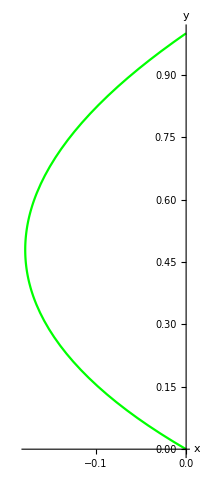

```mathematica
graf11  =ParametricPlot[Table[{x[t],y[t]}/.sol11],{t,0,t11},AxesLabel->{x,y},PlotRange->All,PlotStyle->{Green}]
```

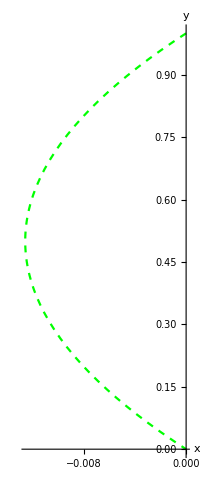

```mathematica
graf21  =ParametricPlot[Table[{x[t],y[t]}/.sol21],{t,0,t21},AxesLabel->{x,y},PlotRange->All,PlotStyle->{Green,Dashed}]
```

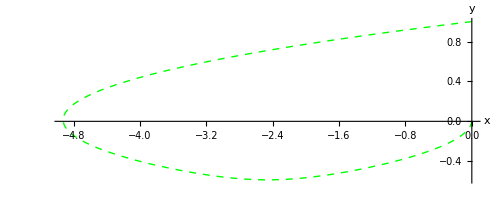

```mathematica
graf31  =ParametricPlot[Table[{x[t],y[t]}/.sol31],{t,0,t31},AxesLabel->{x,y},PlotRange->All,PlotStyle->{Green,Thick,Dashed}]
```

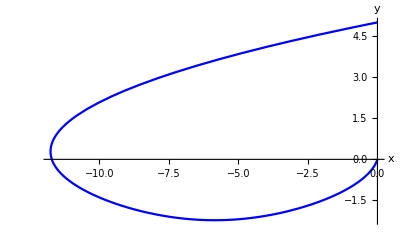

```mathematica
graf12  =ParametricPlot[Table[{x[t],y[t]}/.sol12],{t,0,t12},AxesLabel->{x,y},PlotRange->All,PlotStyle->{Blue}]
```

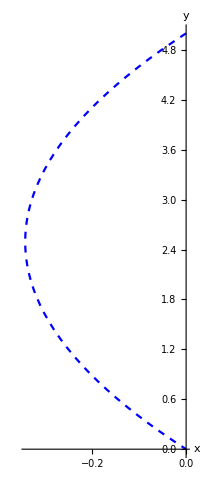

```mathematica
graf22  =ParametricPlot[Table[{x[t],y[t]}/.sol22],{t,0,t22},AxesLabel->{x,y},PlotRange->All,PlotStyle->{Blue,Dashed}]
```

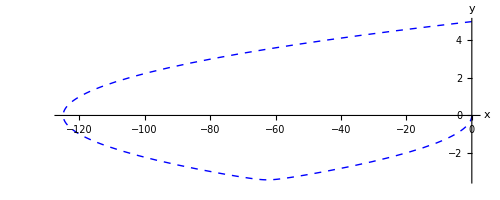

```mathematica
graf32  =ParametricPlot[Table[{x[t],y[t]}/.sol32],{t,0,t32},AxesLabel->{x,y},PlotRange->All,PlotStyle->{Blue,Dashed,Thick}]
```

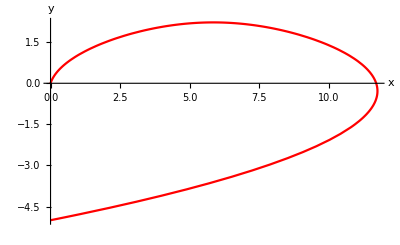

```mathematica
graf13  =ParametricPlot[Table[{x[t],y[t]}/.sol13],{t,0,t13},AxesLabel->{x,y},PlotRange->All,PlotStyle->{Red}]
```

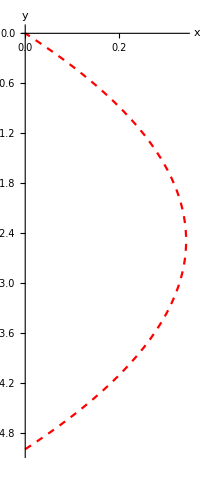

```mathematica
graf23  =ParametricPlot[Table[{x[t],y[t]}/.sol23],{t,0,t23},AxesLabel->{x,y},PlotRange->All,PlotStyle->{Red,Dashed}]
```

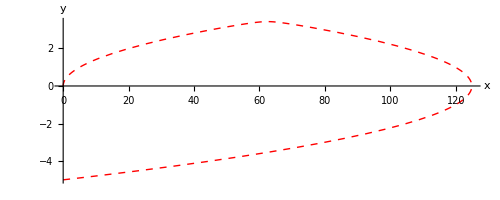

```mathematica
graf33  =ParametricPlot[Table[{x[t],y[t]}/.sol33],{t,0,t33},AxesLabel->{x,y},PlotRange->All,PlotStyle->{Red,Dashed,Thick}]
```

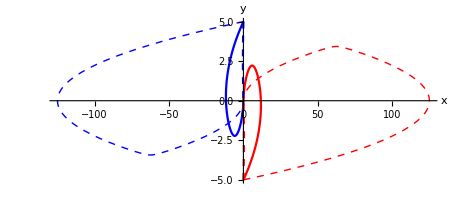

```mathematica
Show[graf12,graf13,graf22,graf23,graf32,graf33]
```

```mathematica
Tabulka0 = Table[{{0,1},{0,5},{0,-5}}]
```

{{0,1},{0,5},{0,-5}}

```mathematica
Tabulka1 = Table[{t11,t12,t13}]
```

{0.114973,1.1225,1.1225}

```mathematica
Tabulka2 = Table[{t21,t22,t23}]
```

{0.100125,0.516374,0.516374}

```mathematica
Tabulka3 = Table[{t31,t32,t33}]
```

{0.236287,1.20564,1.20564}

```mathematica
NumberForm[Grid[{{"Start X/Y","h = 1","h = 10","h = 0.1"},{TableForm[Tabulka0],TableForm[Tabulka1],TableForm[Tabulka2],TableForm[Tabulka3]}},Frame->All],7]
```

Start X/Y | h = 1 | h = 10 | h = 0.1
0 | 1
0 | 5
0 | -5 | 0.1149731
1.122496
1.122496 | 0.1001252
0.5163739
0.5163739 | 0.2362867
1.205635
1.205635

```mathematica
Tabulka11=Table[{β[0]/.sol11,β[0]/.sol12,β[0]/.sol13}]
```

{{5.10615},{4.83431},{1.69272}}

```mathematica
Tabulka22=Table[{β[0]/.sol21,β[0]/.sol22,β[0]/.sol23}]
```

{{4.76228},{4.94928},{1.80769}}

```mathematica
Tabulka33=Table[{β[0]/.sol31,β[0]/.sol32,β[0]/.sol33}]
```

{{4.77172},{4.72411},{1.58252}}

```mathematica
NumberForm[Grid[{{"Start X/Y","h = 1","h = 10","h = 0.1"},{TableForm[Tabulka0],TableForm[Tabulka11],TableForm[Tabulka22],TableForm[Tabulka33]}},Frame->All],7]
```

Start X/Y | h = 1 | h = 10 | h = 0.1
0 | 1
0 | 5
0 | -5 | 5.106146
4.834308
1.692715 | 4.762285
4.94928
1.807687 | 4.771715
4.724114
1.582521